## The problem and the background:

The goal here is to classify reviews collected from the Amazon website in two of the “Positive” and “Negative” classes. Similar to Image and Audio processing in which pixels and sound level values, respectively, are the most basic parts of the data, Characters are the most basic units that create any text. However, we usually use more advanced features in the data such as visual patterns in images or spectrogram values in audio files. It is the same in the text analysis. We use more complex units. The first units that comes into one’s mind are “Word”s. A single word unit is called a Uni-gram. Going more deeper in Natural Language Processing (NLP), we will see that Uni-grams face strong limitations. Two of these limitations are discussed as follow:

1. Some words can have different meanings in different contexts:
Although some words like “Flu” will have almost the same meaning on any context we use it, some other words like “cool” can have multiple meanings base on the context. These meanings will not necessarily be close to each other.

2. Some words can change meanings when combined with other words.
The word “Good” have a positive meaning and usually stands for the fact that object it is describing has a positive or pleasant property. However, when combined with the word “Not” it will turn to the word “Not good” which has the complete opposite meaning.

Therefore, one solution to overcome this issue is to use features which are consisted of N words that are used in the text next to each other.
An example of N-grams for N=1 to 3 for the sentence “The quick brown fox jumped over the lazy dog” is provided as follows:
N=1: {The, quick, fox, jumped, over, the, lazy, dog}
N=2: {The quick, quick fox, fox jumped, jumped over, over the, the lazy, lazy dog}
N=3: {The quick fox, quick fox jumped, fox jumped over, jumped over the, over the lazy, the lazy dog}

In this study, I have used N-grams for N=1 and 2 which are called Uni-grams and Bi-grams, respectively.

### The dataset:

Our dataset is consisted of 400,000 amazon reviews. The length of these reviews can vary. The words used in these reviews can be out of the English dictionary. Each review is labeled with either of “Positive” or “Negative” labels.

### Preprocessing and Feature extraction:

On of the most important parts of every machine learning algorithm is to extract the most relevant features. However, preprocessing is often needed to clear the noise or unneeded parts of the data even before extracting the features.
First, I deleted the first line which was just a legend for the way that data was structured (metadata was deleted)
Here, I observed that the performance doesn’t increase a lot by using the whole data or a reasonable fraction of it. However, the computation time will dramatically decease using just a fraction of data. Therefore, I first downsampled the data using the decimation factor. Next, I removed all the punctuation or stop words from the uni-grams. Please note that since words such as “don’t” are also considered as the stop words, they should not be removed from the bi-grams. After running the code with and without the numbers, it was observed that numbers do not increase the accuracy as well. Therefore, they were also filtered on the preprocessing step.
Next, each string was broken down into words and the top 50 words with the maximum repetition were saved as the uni-gram features. The same process was applied for the bi-grams which gives us 70 integer features in total.
Now we have a MxN matrix, which is called the feature matrix and each row of it (M) represent a review while each column (N) represent the value for the corresponding feature.
I have tried two different ways on assigning the values to the features. First, I said that for each review, each feature will be assigned with “True” if that feature (most repeated uni-gram or bi-gram) was found on the review and will be assigned with “False” otherwise. The, I tried to assign the number of the times that the feature appeared on the review instead of just checking if it was observed or not. It means that each feature will be a number, representing how many times that most repeated uni-gram or bi-gram was present in the review.
Finally, I fed this feature matrix to my classifier.

### Selected algorithms and hypotheses:

I selected K-NN as my third and SVM as my fourth (extra) algorithm. My hypothesis was that K-NN is very fast and doesn’t need much CPU (just need memory) and therefore is a very good choice for real-time applications. Also,  SVM is usually the best choice for binary classification since it divides the hyperspace using the most optimum hyperplane into two different classes. therefore, my second hypothesis was that the accuracy for SVM will outperform all of the others.
As you can see on the results section (at the end of the notebook) all my hypotheses were justified using the simulation results.
Please also note that since the accuracy was not the goal and only comparing the results and knowing what is happening was the main focus, I only used a small portion of data but ran the code for all different cases and provided a comprehensive review of different measurements (including the memory usage and execution time) of all the different algorithms.
Additional information and the discussion over the results are provided at the end of this notebook file.

## The code:

The commented code is provided as follows:

## Part I: Reading the data and preprocessing it

```mathematica
ClearAll;
tic=AbsoluteTime[];
raw=OpenRead[FileNameJoin[{NotebookDirectory[],"reviews.csv"}]];
reviews=Map[StringSplit[#,"|"]&,ReadList[raw,String]];
reviews=Drop[reviews,1];(*drops first line*)
features=ToLowerCase/@reviews[[All,2]];(*make lower case*)
decimationfactor=30;(*10, 15 ,20, 30,40*)
reviews=Take[reviews,{1,-1,decimationfactor}];
features=Take[features,{1,-1,decimationfactor}];
results=reviews[[All,1]];(*results=StringReplace[results,PunctuationCharacter->" "];(*I think it is not needed*)*)
features=StringReplace[features,PunctuationCharacter->" "];
features=StringReplace[features,":"->" "];
(*here we devide bifeatures to be processed later*)
features=DeleteStopwords/@features;
(*delete useless words-takes a lot of time*)
features=Map[StringDelete[DigitCharacter..],features];(*Deleting numbers from the text*)
bifeatures=features;(*This is were bi-gram features seperate from the uni-gram features*)
features=StringSplit[features];(*make string into list of words - mxn : m= reviews n= each word in the review*)
```

```mathematica
This subsection to extracts bi-grams as well
```

bi extracts subsection This to-as grams well

```mathematica
numberofbigramfeatures=20;
bifeatures=StringReplace[bifeatures,PunctuationCharacter->" "];
bifeatures=StringReplace[bifeatures,":"->" "];
joinedstrings=StringJoin[Take[bifeatures,{1,-1,10}]];
```

## Part2: Extracting the features

```mathematica
numberoffeatures=50;
flatfeatures=Flatten[features];(*flatten the whole rows into a one big row*)
wordcount=Counts[flatfeatures];(*create a sorted dictionary with Keys being unique words and values being their repetition*)
sortedkeys=Keys[wordcount];(*extract the sorted keys from the wordcount dictionary*)
themostrepeatedword=sortedkeys[[1;;numberoffeatures]];(*extract the N most repeted words N=1000 here*)
```

### Run this subsection to extract bi-grams as well:

```mathematica
allbigrams=WordCounts[joinedstrings,2];
themostrepeatedbigrams=allbigrams[[1;;numberofbigramfeatures]];
```

## Part3: Forming the feature matrix

```mathematica
t1=AbsoluteTime[];
numberofreviews=Dimensions[features][[1]];
featuresmatrix=ConstantArray[0,{numberofreviews,numberoffeatures+numberofbigramfeatures+1}];
For[j=1,j≤numberoffeatures,j++,(*j is the feature counter and i is the review counter*)
For[i=1,i≤numberofreviews,i++,featuresmatrix[[i,j]]=Count[features[[i,;;]],themostrepeatedword[[j]]]]];
```

```mathematica
For[i=1,i≤numberofreviews,i++, featuresmatrix[[i,-1]]=Length[features[[i]]]];
```

### Run this section to add bi-gram features to the feature matrix

```mathematica
For[i=1,i≤numberofreviews,i++,
tmp00=WordCounts[bifeatures[[i]],2];
For[j=numberoffeatures+1,j≤numberoffeatures+numberofbigramfeatures,j++,
tmp=tmp00[Keys[themostrepeatedbigrams][[j-numberoffeatures]]];
If[IntegerQ[tmp],biCount=tmp,biCount=0];
featuresmatrix[[i,j]]=biCount]];
Dimensions[featuresmatrix];
t2=AbsoluteTime[];
part3time=t2-t1;
```

## Part4: Classifying the data

```mathematica
sampleresults=results[[1;;numberofreviews]];
trainfeaturesmatrix=Drop[featuresmatrix,{1,-1,5}];
testfeaturesmatrix=Take[featuresmatrix,{1,-1,5}];
trainresults=Drop[sampleresults,{1,-1,5}];
testresults=Take[sampleresults,{1,-1,5}];
```

ClassifierFunction[…]

ClassifierMeasurementsObject[…]

0.666292

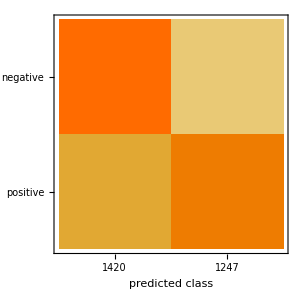

```mathematica
t3=AbsoluteTime[];c=Classify[trainfeaturesmatrix->trainresults,Method->"NeuralNetwork"](*Here you can change the method*)(*NeuralNetwork-NearestNeighbors-RandomForest-SupportVectorMachine*)
cm=ClassifierMeasurements[c,testfeaturesmatrix->testresults]
acc=cm["Accuracy"]
cm["ConfusionMatrixPlot"]
t4=AbsoluteTime[];
part4time=t4-t3;
```

```mathematica
ClassifierInformation[c]
```

Classifier information
Method | Neural network
Number of classes | 2
Number of features | 71
Number of training examples | 10667
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 2
Hidden nodes | ,,504504
Hidden layer activation functions | ,,Rectified LinearRectified Linear
CostFunction | Cost Function

```mathematica
(*tempfile4=FileNameJoin[{NotebookDirectory[],"Results_bigram_30_KNN.wl"}];
Save[tempfile4,{trainfeaturesmatrix,testfeaturesmatrix,trainresults,testresults,c,cm,part4time,acc}];*)
toc=AbsoluteTime[];
Runtimemins=(toc-tic)/60
```

2.26056397

## Results:

Accuracy is: 0.666292

Precision to Recall ratio is: 1.09302

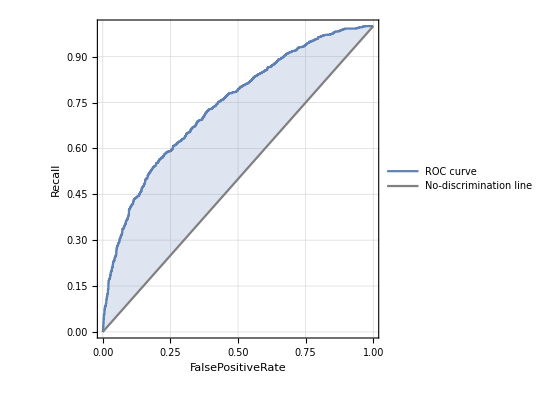

```mathematica
accuracy=cm["Accuracy"];
Print["Accuracy is: ",accuracy]
PrectoRecall=cm["Precision"][[2]]/cm["Recall"][[2]];
Print["Precision to Recall ratio is: ",PrectoRecall]
cm["ROCCurve"][[2]](*The ROC Curve for the Positive class*)
```

## Loading all the results - Please note that you need to download saved files for this section:

### Displaying results for all the methods

The results for the Randon Forest Algorithm:

Accuracy is: 0.67775

Precision to Recall ratio is: 1.01733

Filesize in MegaBytes: 23.8834

Execution (Train+Test) time (mins): 20.76520701

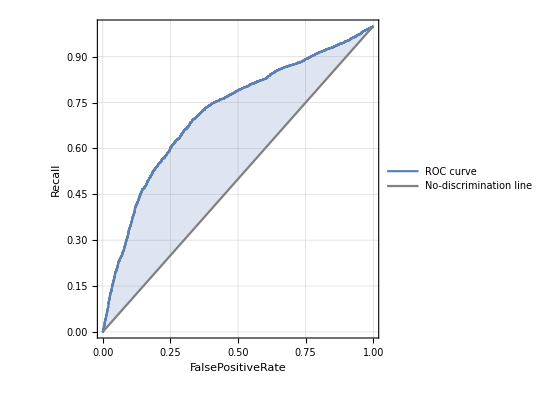

The results for the Neural Networks Algorithm:

Accuracy is: 0.67475

Precision to Recall ratio is: 0.966586

Filesize in MegaBytes: 29.0351

Execution (Train+Test) time (mins): 2.00427258

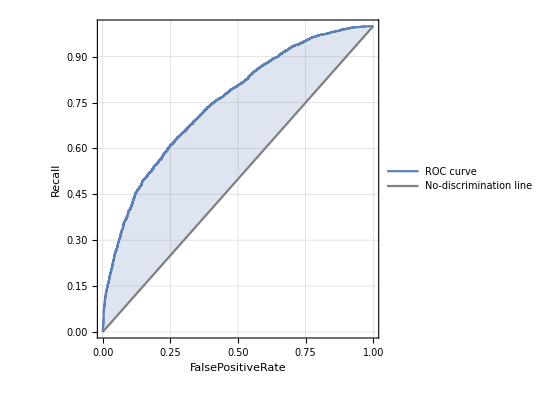

The results for the K-Nearest Neighbors Algorithm:

Accuracy is: 0.658875

Precision to Recall ratio is: 1.01397

Filesize in MegaBytes: 115.433

Execution (Train+Test) time (mins): 0.18808744

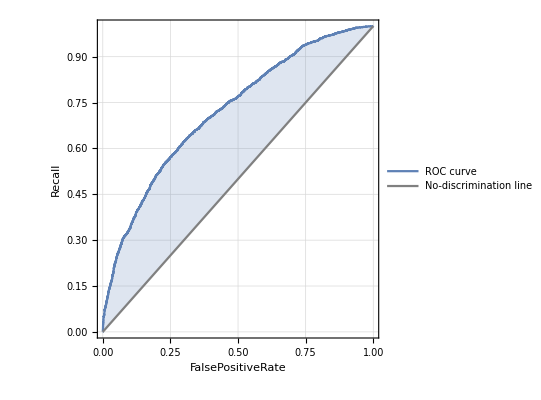

The results for the Support Vector Machine Algorithm:

Accuracy is: 0.68075

Precision to Recall ratio is: 1.20531

Filesize in MegaBytes: 91.7944

Execution (Train+Test) time (mins): 6.819625498

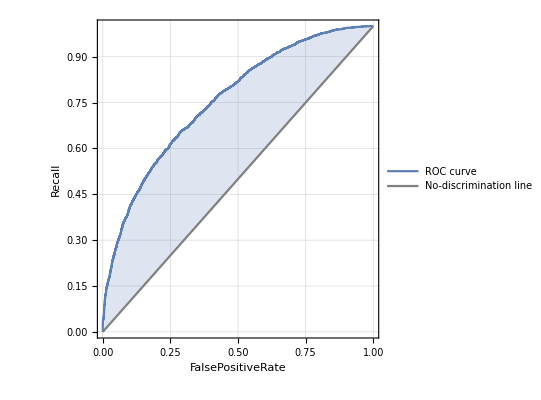

```mathematica
Clear All;
Print["The results for the Randon Forest Algorithm: "]
tempfile=FileNameJoin[{NotebookDirectory[],"Results_bigram_10_RF.wl"}];
Get[tempfile];
accuracy=cm["Accuracy"];
Print["Accuracy is: ",accuracy]
PrectoRecall=cm["Precision"][[2]]/cm["Recall"][[2]];
Print["Precision to Recall ratio is: ",PrectoRecall]
filesize=N[FileByteCount[tempfile]/(10^6)];
Print["Filesize in MegaBytes: ",filesize]
executiontime=part4time/60;
Print["Execution (Train+Test) time (mins): ",executiontime]
cm["ROCCurve"][[2]]

Clear All;
Print["The results for the Neural Networks Algorithm: "]
tempfile=FileNameJoin[{NotebookDirectory[],"Results_bigram_10_NN.wl"}];
Get[tempfile];
accuracy=cm["Accuracy"];
Print["Accuracy is: ",accuracy]
PrectoRecall=cm["Precision"][[2]]/cm["Recall"][[2]];
Print["Precision to Recall ratio is: ",PrectoRecall]
filesize=N[FileByteCount[tempfile]/(10^6)];
Print["Filesize in MegaBytes: ",filesize]
executiontime=part4time/60;
Print["Execution (Train+Test) time (mins): ",executiontime]
cm["ROCCurve"][[2]]

Clear All;
Print["The results for the K-Nearest Neighbors Algorithm: "]
tempfile=FileNameJoin[{NotebookDirectory[],"Results_bigram_10_KNN.wl"}];
Get[tempfile];
accuracy=cm["Accuracy"];
Print["Accuracy is: ",accuracy]
PrectoRecall=cm["Precision"][[2]]/cm["Recall"][[2]];
Print["Precision to Recall ratio is: ",PrectoRecall]
filesize=N[FileByteCount[tempfile]/(10^6)];
Print["Filesize in MegaBytes: ",filesize]
executiontime=part4time/60;
Print["Execution (Train+Test) time (mins): ",executiontime]
cm["ROCCurve"][[2]]

Clear All;
Print["The results for the Support Vector Machine Algorithm: "]
tempfile=FileNameJoin[{NotebookDirectory[],"Results_bigram_10_SVM.wl"}];
Get[tempfile];
accuracy=cm["Accuracy"];
Print["Accuracy is: ",accuracy]
PrectoRecall=cm["Precision"][[2]]/cm["Recall"][[2]];
Print["Precision to Recall ratio is: ",PrectoRecall]
filesize=N[FileByteCount[tempfile]/(10^6)];
Print["Filesize in MegaBytes: ",filesize]
executiontime=part4time/60;
Print["Execution (Train+Test) time (mins): ",executiontime]
cm["ROCCurve"][[2]]
```

### Comparing results for all different methods (doesn’t need to download any files)

### Table of all the measurements:

```mathematica
m={{" ","RF","NN","K-NN","SVM"},
{"Accuracy (%):",100*0.67775,100*0.674,100*0.658,100*0.680},
{"100 x Precision/Recall:",100*1.017, 100*0.966,100*1.013, 100*1.205},
{"File size (mb):",23.883, 29.035,115.433, 91.794},
{"Execution time (mins):",20.765, 2.004,0.188, 6.819}
};
Grid[m,Frame->All]
```

| RF | NN | K-NN | SVM
Accuracy (%): | 67.775 | 67.4 | 65.8 | 68.
100 x Precision/Recall: | 101.7 | 96.6 | 101.3 | 120.5
File size (mb): | 23.883 | 29.035 | 115.433 | 91.794
Execution time (mins): | 20.765 | 2.004 | 0.188 | 6.819

#### The comparison plots:

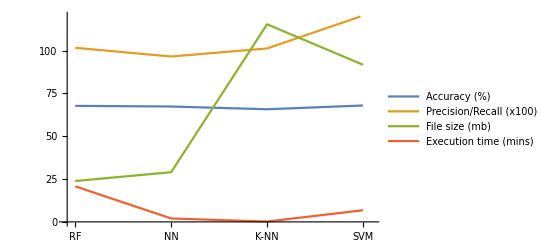

```mathematica
ListLinePlot[m[[2;;-1,2;;-1]],PlotRange->{{.9,4.1},{0,120}},PlotLegends->{"Accuracy (%)","Precision/Recall (x100)","File size (mb)","Execution time (mins)"},Ticks->{{{1,"RF"},{2,"NN"},{3,"K-NN"},{4,"SVM"}},Automatic}]
```

### Discussion:

In this part, I am going to discuss all my hypothesis and observations on different measurements illustrated on the previous subsection.

#### Accuracy:

It is known that for a binary classification problem,SVM is usually the best choice for binary classification since it divides the hyperspace using the most optimum hyperplane into two different classes. There is no surprise that it did best compare to all the other techniques used.
NN and RF performed almost the same. However, NN was way faster than RF which makes it a better choice for this problem. We will talk more about this on the Execution time subsection. K-NN is showing the less accuracy. However, with having an eye on the execution time and it’s slight different with other methods in accuracy, it might be an ideal method for applications with limited CPU power (However, it needs more memory space).

#### File Size:

The K-NN algorithm needs to save all the data so that it’s file size is larger than all other methods. SVM also needs to save a partition of the data which are constructing the boundaries (Support Vectors) and therefore has the second largest file size. Neural Networks and RF only need to save the network wrights and the decision tree respectively and therefore do not use much memory when saved.

#### Precision to Recall Ratio:

Precession is defined as TP/(TP+FP) or in other words, is showing how many of the selected items are relevant. Recall, on the other hand, is defined as TP/(TP+FN) or in other words, is showing how many of relevant items are selected. If we divide precision to recall, we will have (TP+FN)/(TP+FP). Therefore, if we have equal FN and FP, the Precision to Recall ratio will be equal to one. Therefore, for unweighted classes, a precision to recall ratio of about one is usually a desired ratio. in all of the methods used here, we had a precision to recall ratio of around one, except the SVM method which shows a tendency toward the positive class.

#### ROC Curve

Receiver Operating Characteristics (ROC) curve is a graphical plot that illustrates the diagnostic ability of a binary classifier system as its discrimination threshold is varied. The ROC curve is created by plotting the true positive rate (TPR) or often Recall (TP/(TP+FN)) against the false positive rate (FPR) at various threshold settings. The best threshold is only a function on the weight that a specific problem assigns different cases (TP, FP, TN, FN). For example, in a radar problem, if the radar detects an enemy fighter jet while there is no fighter (FP), it is just a simple false alarm and no extreme harm will be caused. But if there is a jet and the radar fails to detect it (FN) it might end up with a disaster. Therefore, for this specific example, the threshold will be set such that the probability of false negative gets as small as possible.
For the example studied here (dataset 3) since the weight of the two classes are the same (Also their prior is the same as I counted the number of the positive and negative reviews and they were almost the same, which means, the chance level for this classification is %50), selecting threshold in a way that the ROC curve has the maximum distance than the no-discrimination line will be the best choice.

#### Execution time (Train+Test):

K-NN only compares each test data with the K nearest neighbors in the feature space and therefore it is pretty fast and useful for the real-time applications. Neural Networks are very fast in running but training them can take some time and as we can see here, NN is the second fastest algorithm among all the tested ones. RF needs to form the decision tree using all the data and therefore, the size of this search space can increase dramatically when the input data is large. SVM needs to find kernels to map the complex space into a one with linearly separable feature distribution. Therefore, it can take sometime when applied to a set of features which are distributed in a non linear fashion on the feature space. RF was the slowest algorithm among all of the tested ones.

### Take home messages:

I believe the take home messages from this study can be listed as follows:

1. Feature selection is one of the most important parts of every machine learning algorithm
2. Not all the train data is needed and an algorithm can be trained with a fraction of data if the pattern is well represented on that fraction
3. Pre-processing and filtering the data can increase accuracy and also increase the speed of the algorithm
4. Different machine learning algorithms has their own pros and cons, some use more CPU, some use more memory and some are faster while some other are more accurate. But the most important lesson here is that al the above mentioned measures can vary depending on the nature of the data. i.e. some methods work better in a specific types of data. For example, SVM is very good in binary classification but might not be as good in multi-class classification.
	4.1. In this study, the fastest algorithms were K-NN and NN
	4.2. In this study, NN and RF were using the smallest memory size when saved
	4.3. In this binary (two-class) classification problem, SVM had the best performance